```mathematica
Get["new1through5Sequential.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Get["OG_Josh_o1through4.m"]
```

```mathematica
For[k = 0, k ≤4,k++,
Josh[k] = Exp[γ  (y  - x)]* Sum[(-1/2)^j (γ)^(2j) * o[j], {j, 0, k}]
]
```

```mathematica
Clear[o]
```

```mathematica
GaussianApprox= (2 π x (1-x) t)^(-1/2) Exp[-(y-(x+2Ne α Λ x (1-x) t / W))^2 / (2 x (1-x) t)]
```

(ⅇ^(-(-x+y-(2 Ne t (1-x) x α Λ)/W)^2/(2 t (1-x) x)))/(√(2 π) √(t (1-x) x))

```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
neutral = Kimura[x,y,t,10];
```

```mathematica
kimplot = Kimura[x,y,t,n];
```

```mathematica
Plot[Evaluate[Table[kimplot /. {x-> 0.25, t-> 0.1}, {n,1,11,2}]],{y,0,1},PlotLegends->{Table[n,{n,1,11,2}]},
PlotLabels->Table[TextString[n],{n,1,11,2}], PlotStyle-> ColorData[{"StarryNightColors",{1,6}}]]
```

-Graphics-

```mathematica
kthkimura[x_,y_,t_,m_] := 4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t];
```

```mathematica
kythplot = kthkimura[x,y,t,n];
```

```mathematica
Plot[Evaluate[Table[kythplot /. {x-> 0.25, t-> 0.1}, {n,1,5}]],{y,0,1},PlotLegends->{Table[n,{n,1,5}]},
PlotLabels->Table[TextString[n],{n,1,5}]]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\firstkkimura.svg",%15,"SVG"]
```

C:\Users\natha\Documents\firstkkimura.svg

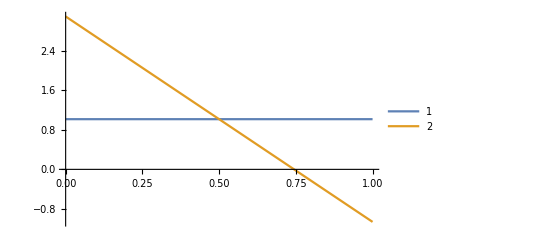

```mathematica
Plot[{Kimura[x,y,t,1] /. {x-> 0.25, t-> 0.1},Kimura[x,y,t,2] /. {x-> 0.25, t-> 0.1}},{y,0,1},PlotLegends->{"1","2"}]
```

```mathematica
Plot[Evaluate[Table[kimplot /. {x-> 0.25, t-> 0.1}, {n,1,5}]],{y,0,1},PlotLegends->{Table[n,{n,1,5}]},
PlotLabels->Table[TextString[n],{n,1,5}]]
```

-Graphics-

```mathematica
Clear[Anim];
Anim=Table[Plot[Evaluate[kimplot/. {x->0.25,t-> 0.1,n->bigN}],
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"n=",bigN}, 
PlotRange->{{0,1},{0,5}}],{bigN,1,15}]
```

```mathematica
Export["neutralConvergence.gif",Anim,"DisplayDurations"->0.75]
```

neutralConvergence.gif

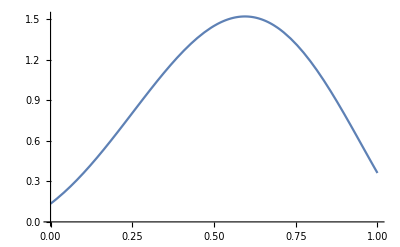

```mathematica
Plot[Evaluate[SimplifiedHayward[3]/.{x->0.5, t->0.25,Ne->500,α->.001,Λ->1,W->1, VG->0.0001111}],{y,0,1}]
```

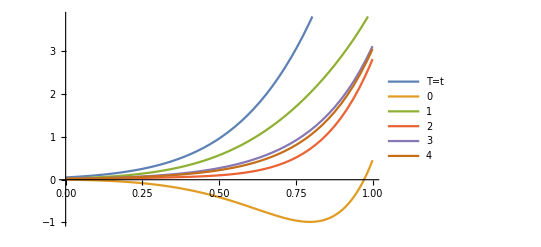

```mathematica
Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->0.5, t->0.5,Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

```mathematica
Table[TextString[k],{k,0,5}]
```

{0,1,2,3,4,5}

```mathematica
First[{"0","1","2","3","4","5"}]
```

0

```mathematica
Clear[Anim]
```

```mathematica
NumberForm
```

```mathematica
Anim=Table[Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->0.5,t-> 0.1,Ne->500, Λ -> 1, W->1, VG->.00001111},{k,0, 5}]],
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"α=",NumberForm[α, {6,5}]}, 
PlotLabels->Table[TextString[k],{k,0,5}],
PlotRange->{{0,1},{0,10}}],{α,.0001,.01,.00025}];
```

```mathematica
Export["selectionConvergence.gif",Anim,"DisplayDurations"->0.3]
```

selectionConvergence.gif

```mathematica
Length[Anim]
```

40

```mathematica
Anim[[40]]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\BigAlphaConvergence.svg",%59,"SVG"]
```

C:\Users\natha\Documents\BigAlphaConvergence.svg

```mathematica
Anim=Table[Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->0.5,Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{k,0, 5}]],
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"T=",t}, 
PlotLabels->Table[TextString[k],{k,0,5}],
PlotRange->{{0,1},{-10,10}}],{t,.001,.5,.025}];
```

```mathematica
Export["TimeConvergence.gif",Anim,"DisplayDurations"->0.75]
```

TimeConvergence.gif

```mathematica
Anim[[1]]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\smallTimeConvergence.svg",%37,"SVG"]
```

C:\Users\natha\Documents\smallTimeConvergence.svg

```mathematica
Length[Anim]
```

20

```mathematica
Anim[[20]]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\longTimeConvergence.svg",%40,"SVG"]
```

C:\Users\natha\Documents\longTimeConvergence.svg

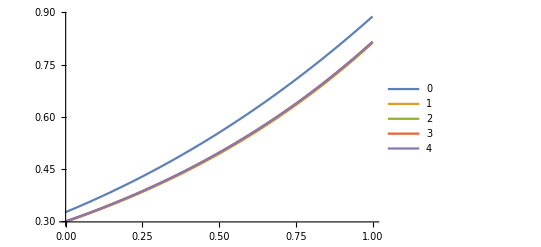

```mathematica
Plot[Evaluate[Table[Josh[k]/. {x->0.5, t->1,γ->1},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,4}]}]
```

```mathematica
Clear[blah];
blah=NDSolve[{D[g[x,t],t] == -(2 Ne α Λ / W) Exp[2 Ne VG t / W]*x*(1-x)*D[g[x,t],x]+1/2*x*(1-x)*D[g[x,t],{x,2}],
g[x,0]==Evaluate[PDF[TriangularDistribution[{0.4999,0.5001},0.5],x]x(1-x)],
g[0,t]==0,
g[1,t]==0}/.{α->.005,Λ->1,W->1, VG->0.00001111, Ne ->500},
g,{x,0,1},{t,0.001,1},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

```mathematica
Plot[{SimplifiedHayward[2] /. {x->0.5,t -> 0.001, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111}, GaussianApprox/. {x->0.5,t -> 0.001, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},
g[x,t] /(x(1-x)) /.blah /.{t->0.001, x->y}}, {y,0,1}, PlotLabels->{"Perturb", "Gaussian", "Numerical"}]
```

-Graphics-

```mathematica
tmp[y_,t_] = Evaluate[GaussianApprox /. {x->0.5, Ne->500,α->0.005, Λ -> 1, W->1}];
joshtmp[y_,t_] = Evaluate[Josh[3]/.{x->0.5,γ->5}];
haywardtmp[y_,t_,VG_] = Evaluate[SimplifiedHayward[3]/. {x->0.5,Ne->500,α->0.005, Λ -> 1, W->1}];
```

```mathematica
Clear[Anim];
Anim=Table[Plot[{haywardtmp[y,t,0.00001111],joshtmp[y,t],tmp[y,t]},
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"T=",t}, 
PlotLabels->{"Hayward","Josh", "Gaussian"},
PlotRange->{{0,1},{-5,5}}],
{t,.001,.5,.025}]
```

```mathematica
Export["TimeComparison.gif",Anim,"DisplayDurations"->0.75]
```

```mathematica
Plot[{haywardtmp[y,0.25,0.00001111],joshtmp[y,0.25],tmp[y,0.25]},
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLabels->{"Hayward","Josh", "Gaussian"},
PlotLegends->TextString@Row@{"T=",0.25}, 
PlotRange->{{0,1},{-1,4}}]
```

-Graphics-

```mathematica
Clear[Anim];
Anim=Table[Plot[{haywardtmp[y,0.1,VG],joshtmp[y,0.1],tmp[y,0.1]},
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"VG=",NumberForm[VG, {6,5}]}, 
PlotLabels->{"Hayward","Josh", "Gaussian"},
PlotRange->{{0,1},{0,10}}],
{VG,.000011111,.11111, 0.005}]
```

```mathematica
Export["VGComparison.gif",Anim,"DisplayDurations"->0.75]
```

VGComparison.gif

```mathematica
Export["C:\\Users\\natha\\Documents\\25gencomparison.svg",%59,"SVG"]
```

C:\Users\natha\Documents\25gencomparison.svg

```mathematica
Export["C:\\Users\\natha\\Documents\\10gencomparison.svg",%54,"SVG"]
```

C:\Users\natha\Documents\10gencomparison.svg

```mathematica
Export["C:\\Users\\natha\\Documents\\5gencomparison.svg",%51,"SVG"]
```

C:\Users\natha\Documents\5gencomparison.svg

```mathematica
Export["C:\\Users\\natha\\Documents\\1gencomparison.svg",%43,"SVG"]
```

C:\Users\natha\Documents\1gencomparison.svg

```mathematica
Manipulate[Plot[tmp[y,t], {y,0,1}], {t,0.01,1}]
```

```mathematica
Manipulate[Plot[joshtmp[y,t],{y,0,1}],{t,0.01,1}]
```

```mathematica
Manipulate[Plot[haywardtmp[y,t,VG],{y,0,1}],{t,0.01,1},{VG,.0000011111,.11111}, ContinuousAction->False]
```

```mathematica
Manipulate[Plot[{joshtmp[y,t],tmp[y,t]},{y,0,1},PlotLabels->{"Josh", "Gaussian"}],{t,0.01,1}]
```

```mathematica
Manipulate[Plot[{haywardtmp[y,t,VG],joshtmp[y,t],tmp[y,t]},{y,0,1},PlotLabels->{"Hayward","Josh", "Gaussian"}],{t,0.01,1},{VG,.0000011111000001,.11111000001}, ContinuousAction->False]
```

```mathematica
2 20000 .005^2
```

1.

```mathematica
2 500 0.00025
```

0.25

```mathematica
l = {}
```

{}

```mathematica
Do[AppendTo[l,{i,j,i+j}];
Print[l],{i,{1,2,3}},{j,{1,2,3}}]
```

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4},{2,1,3}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6}}

```mathematica
1/20000
```

1/20000

```mathematica
N[1/20000]
```

0.00005

```mathematica
Clear[out];
out = {{"mult","alpha","VG","expectation","thresh","totalP","Pdetected","Pnotdetected
"}};
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
time = 0.25;
selectedNe = 500;
jumpSize = 1;
SelCoef = 0.002;
sigCutoff = 0.99;
```

```mathematica
out
```

{{mult,alpha,VG,expectation,thresh,totalP,Pdetected,Pnotdetected
}}

```mathematica
Do[Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected];
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe,α->SelCoef},
g,{x,0,1},MaxStepSize->.000025];
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}];
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}];
expectation = mult * expectation;
Print[expectation];
expectation  = expectation[[1]][[1]];
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}];
thresh = Solve[tmp == (sigCutoff - pNeutFix) && 0<Ψ<1, {Ψ}, Reals];
Print[thresh];
If[Length[thresh] != 1,Throw[{α, VG, thresh}]];
Ψ = Ψ /. thresh;
Print[Ψ];
totalP = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,α->SelCoef},{y, 0,1}];
Pdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,α->SelCoef},{y, Min[expectation+Ψ,1],1}];
Pnotdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,α->SelCoef},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}];
AppendTo[out,{mult,SelCoef,VG,expectation,Ψ[[1]],totalP,Pdetected,Pnotdetected}],
{mult, {0.5,1,1.5,2,3}},
{VG, {.101, .0101, .00101}}
]
```

{{0.042391}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.398735}}

{0.398735}

{{0.042391}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.398735}}

{0.398735}

{{0.042391}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
out
```

{{mult,alpha,VG,expectation,thresh,totalP,Pdetected,Pnotdetected
},{0.5,0.002,0.101,0.042391,0.398735,0.306133,0.0102821,0.295851},{0.5,0.002,0.0101,0.042391,0.398735,0.332285,0.0137169,0.318568},{0.5,0.002,0.00101,0.042391,0.398735,0.357752,0.0224461,0.335306},{1,0.002,0.101,0.0847821,0.470244,0.523666,0.0103516,0.513315},{1,0.002,0.0101,0.0847821,0.470244,0.558678,0.0144629,0.544215},{1,0.002,0.00101,0.0847821,0.470244,0.591853,0.0249896,0.566864},{1.5,0.002,0.101,0.127173,0.509489,0.676659,0.0104025,0.666257},{1.5,0.002,0.0101,0.127173,0.509489,0.71136,0.0149304,0.69643},{1.5,0.002,0.00101,0.127173,0.509489,0.743548,0.0264083,0.71714},{2,0.002,0.101,0.169564,0.532963,0.782987,0.0104407,0.772547},{2,0.002,0.0101,0.169564,0.532963,0.813115,0.0152294,0.797885},{2,0.002,0.00101,0.169564,0.532963,0.840796,0.0271904,0.813606},{3,0.002,0.101,0.254346,0.551187,0.904729,0.0104795,0.894249},{3,0.002,0.0101,0.254346,0.551187,0.922941,0.0154645,0.907477},{3,0.002,0.00101,0.254346,0.551187,0.940797,0.02746,0.913337}}

```mathematica
Export["mult_VG.csv",out,"csv"];
```

```mathematica
mult = 2
VG = .00101
SelCoef = 0.002
```

2

0.00101

0.002

```mathematica
Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected]
```

```mathematica
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe,α->SelCoef},
g,{x,0,1},MaxStepSize->.000025]
```

{{g→InterpolatingFunction[{{0., 1.}}, <>]}}

```mathematica
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}]
```

{5.71699}

```mathematica
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}]
```

{{0.0847821}}

```mathematica
expectation = mult * expectation
```

{{0.169564}}

```mathematica
Print[expectation]
```

{{0.169564}}

```mathematica
expectation  = expectation[[1]][[1]]
```

0.169564

```mathematica
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}]
```

0.777787

```mathematica
pNeutFix = 1- neutAUC
```

0.222213

```mathematica
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}]
```

-2.55844 Max[0,0.169564-Ψ]+1.60231 Max[0,0.169564-Ψ]^2+4.29029 Max[0,0.169564-Ψ]^3-8.81128 Max[0,0.169564-Ψ]^4+6.42222 Max[0,0.169564-Ψ]^5-1.15334 Max[0,0.169564-Ψ]^6-1.3352 Max[0,0.169564-Ψ]^7+1.04908 Max[0,0.169564-Ψ]^8-0.323729 Max[0,0.169564-Ψ]^9+0.0403102 Max[0,0.169564-Ψ]^10+2.55844 Min[1,0.169564+Ψ]-1.60231 Min[1,0.169564+Ψ]^2-4.29029 Min[1,0.169564+Ψ]^3+8.81128 Min[1,0.169564+Ψ]^4-6.42222 Min[1,0.169564+Ψ]^5+1.15334 Min[1,0.169564+Ψ]^6+1.3352 Min[1,0.169564+Ψ]^7-1.04908 Min[1,0.169564+Ψ]^8+0.323729 Min[1,0.169564+Ψ]^9-0.0403102 Min[1,0.169564+Ψ]^10

```mathematica
thresh = Solve[tmp == (sigCutoff - pNeutFix) && 0<Ψ<1, {Ψ}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.532963}}

```mathematica
Print[thresh]
```

{{Ψ→0.532963}}

```mathematica
If[Length[thresh] != 1,Throw[{α, VG, thresh}]]
```

```mathematica
Ψ = Ψ /. thresh
```

{0.532963}

```mathematica
Print[Ψ]
```

{0.532963}

```mathematica
totalP = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,α->SelCoef},{y, 0,1}]
```

0.840796

```mathematica
Pdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,α->SelCoef},{y, Min[expectation+Ψ,1],1}]
```

0.0271904

```mathematica
Pnotdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,α->SelCoef},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

0.813606

```mathematica
Clear[out];
out = {{"start","alpha","VG","expectation","thresh","totalP","Pdetected","Pnotdetected
"}};
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
time = 0.25;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
genVar = 0.0101;
```

```mathematica
out
```

{{start,alpha,VG,expectation,thresh,totalP,Pdetected,Pnotdetected
}}

```mathematica
Do[Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected];
expectation = start;
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}];
thresh = Solve[tmp == (sigCutoff - pNeutFix) && 0<Ψ<1, {Ψ}, Reals];
Print[thresh];
If[Length[thresh] != 1,Throw[{α, VG, thresh}]];
Ψ = Ψ /. thresh;
Print[Ψ];
totalP = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{y, 0,1}];
Pdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{y, Min[expectation+Ψ,1],1}];
Pnotdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}];
AppendTo[out,{start,α,genVar,expectation,Ψ[[1]],totalP,Pdetected,Pnotdetected}],
{α, {0.00025, 0.0005, 0.00075,0.001,0.002,0.005}},
{start, {0.05,0.1,0.15,0.2,0.25}}
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.415836}}

{0.415836}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.486736}}

{0.486736}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{Ψ→0.523644}}

{0.523644}

{{Ψ→0.543231}}

{0.543231}

{{Ψ→0.55098}}

{0.55098}

{{Ψ→0.415836}}

{0.415836}

{{Ψ→0.486736}}

{0.486736}

{{Ψ→0.523644}}

{0.523644}

{{Ψ→0.543231}}

{0.543231}

{{Ψ→0.55098}}

{0.55098}

{{Ψ→0.415836}}

{0.415836}

{{Ψ→0.486736}}

{0.486736}

{{Ψ→0.523644}}

{0.523644}

{{Ψ→0.543231}}

{0.543231}

{{Ψ→0.55098}}

{0.55098}

{{Ψ→0.415836}}

{0.415836}

{{Ψ→0.486736}}

{0.486736}

{{Ψ→0.523644}}

{0.523644}

{{Ψ→0.543231}}

{0.543231}

{{Ψ→0.55098}}

{0.55098}

{{Ψ→0.415836}}

{0.415836}

{{Ψ→0.486736}}

{0.486736}

{{Ψ→0.523644}}

{0.523644}

{{Ψ→0.543231}}

{0.543231}

{{Ψ→0.55098}}

{0.55098}

{{Ψ→0.415836}}

{0.415836}

{{Ψ→0.486736}}

{0.486736}

{{Ψ→0.523644}}

{0.523644}

{{Ψ→0.543231}}

{0.543231}

{{Ψ→0.55098}}

{0.55098}

```mathematica
out
```

{{start,alpha,VG,expectation,thresh,totalP,Pdetected,Pnotdetected
},{0.05,0.00025,0.0101,0.05,0.415836,0.349964,0.0104247,0.339539},{0.1,0.00025,0.0101,0.1,0.486736,0.583873,0.0105002,0.573373},{0.15,0.00025,0.0101,0.15,0.523644,0.738021,0.0105457,0.727475},{0.2,0.00025,0.0101,0.2,0.543231,0.838039,0.0105738,0.827465},{0.25,0.00025,0.0101,0.25,0.55098,0.90181,0.0105889,0.891221},{0.05,0.0005,0.0101,0.05,0.415836,0.354139,0.0108658,0.343273},{0.1,0.0005,0.0101,0.1,0.486736,0.58917,0.0110229,0.578147},{0.15,0.0005,0.0101,0.15,0.523644,0.742974,0.0111177,0.731857},{0.2,0.0005,0.0101,0.2,0.543231,0.842077,0.0111761,0.830901},{0.25,0.0005,0.0101,0.25,0.55098,0.904823,0.0112072,0.893616},{0.05,0.00075,0.0101,0.05,0.415836,0.358337,0.0113239,0.347013},{0.1,0.00075,0.0101,0.1,0.486736,0.594458,0.0115686,0.58289},{0.15,0.00075,0.0101,0.15,0.523644,0.747881,0.0117164,0.736165},{0.2,0.00075,0.0101,0.2,0.543231,0.846039,0.0118071,0.834231},{0.25,0.00075,0.0101,0.25,0.55098,0.907738,0.0118546,0.895883},{0.05,0.001,0.0101,0.05,0.415836,0.362558,0.0117994,0.350759},{0.1,0.001,0.0101,0.1,0.486736,0.599734,0.0121378,0.587597},{0.15,0.001,0.0101,0.15,0.523644,0.752733,0.0123421,0.740391},{0.2,0.001,0.0101,0.2,0.543231,0.849905,0.0124664,0.837438},{0.25,0.001,0.0101,0.25,0.55098,0.910518,0.0125298,0.897988},{0.05,0.002,0.0101,0.05,0.415836,0.379641,0.0138824,0.365758},{0.1,0.002,0.0101,0.1,0.486736,0.620612,0.0146545,0.605957},{0.15,0.002,0.0101,0.15,0.523644,0.77133,0.0151089,0.756221},{0.2,0.002,0.0101,0.2,0.543231,0.863909,0.0153642,0.848544},{0.25,0.002,0.0101,0.25,0.55098,0.919383,0.0154627,0.90392},{0.05,0.005,0.0101,0.05,0.415836,0.431759,0.0219923,0.409767},{0.1,0.005,0.0101,0.1,0.486736,0.67724,0.024396,0.652844},{0.15,0.005,0.0101,0.15,0.523644,0.810934,0.0253761,0.785558},{0.2,0.005,0.0101,0.2,0.543231,0.876884,0.0253975,0.851486},{0.25,0.005,0.0101,0.25,0.55098,0.901041,0.024688,0.876353}}

```mathematica
Export["alpha_start.csv",out,"csv"];
```

```mathematica
Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected]
```

```mathematica
α=0.00025
start = 0.05
```

0.00025

0.05

```mathematica
expectation = start
```

0.05

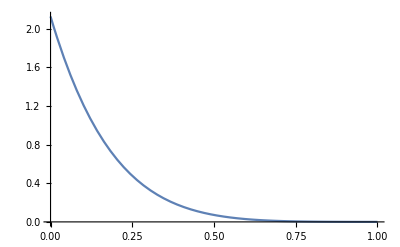

```mathematica
Plot[neutral/. {x->expectation, t->time}, {y,0,1}]
```

```mathematica
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}]
```

0.345813

```mathematica
pNeutFix = 1- neutAUC
```

0.654187

```mathematica
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}]
```

-2.12687 Max[0.,0.05-1. Ψ]+5.72515 Max[0.,0.05-1. Ψ]^2-8.7815 Max[0.,0.05-1. Ψ]^3+8.27943 Max[0.,0.05-1. Ψ]^4-4.64948 Max[0.,0.05-1. Ψ]^5+1.09561 Max[0.,0.05-1. Ψ]^6+0.439026 Max[0.,0.05-1. Ψ]^7-0.473448 Max[0.,0.05-1. Ψ]^8+0.171254 Max[0.,0.05-1. Ψ]^9-0.0249833 Max[0.,0.05-1. Ψ]^10+2.12687 Min[1.,0.05+Ψ]-5.72515 Min[1.,0.05+Ψ]^2+8.7815 Min[1.,0.05+Ψ]^3-8.27943 Min[1.,0.05+Ψ]^4+4.64948 Min[1.,0.05+Ψ]^5-1.09561 Min[1.,0.05+Ψ]^6-0.439026 Min[1.,0.05+Ψ]^7+0.473448 Min[1.,0.05+Ψ]^8-0.171254 Min[1.,0.05+Ψ]^9+0.0249833 Min[1.,0.05+Ψ]^10

```mathematica
thresh = Solve[tmp == (sigCutoff - pNeutFix) && 0<Ψ<1, {Ψ}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.415836}}

```mathematica
Print[thresh]
```

{{Ψ→0.415836}}

```mathematica
If[Length[thresh] != 1,Throw[{α, VG, thresh}]]
```

```mathematica
Ψ = Ψ /. thresh
```

{0.415836}

```mathematica
Print[Ψ]
```

{0.415836}

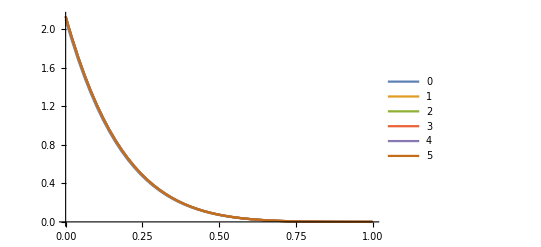

```mathematica
Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->expectation,t ->time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

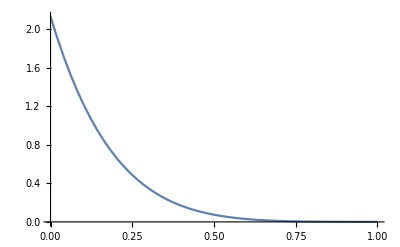

```mathematica
Plot[Evaluate[SimplifiedHayward[3]/. {x->expectation,t ->time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar}],{y,0,1}]
```

```mathematica
FindMinimum[Evaluate[SimplifiedHayward[3]/.{x->expectation,t -> 0.25, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar}],{y,0,1}]
```

{0.0000101365,{y→1.03183}}

```mathematica
totalP = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{y, 0,1}]
```

0.349964

```mathematica
Pdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{y, Min[expectation+Ψ,1],1}]
```

0.0104247

```mathematica
Pnotdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

0.339539

```mathematica
Clear[out];
out = {{"mult","alpha","VG","expectation","thresh","totalP","Pdetected","Pnotdetected
"}};
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
time = 0.25;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
genVar = 0.0101;
```

```mathematica
out
```

{{mult,alpha,VG,expectation,thresh,totalP,Pdetected,Pnotdetected
}}

```mathematica
Do[Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected];
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe},
g,{x,0,1},MaxStepSize->.000025];
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}];
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}];
Print[expectation];
expectation  = expectation[[1]][[1]];
expectation = mult * expectation;
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}];
thresh = Solve[tmp == (sigCutoff - pNeutFix) && 0<Ψ<1, {Ψ}, Reals];
Print[thresh];
If[Length[thresh] != 1,Throw[{α, VG, thresh}]];
Ψ = Ψ /. thresh;
Print[Ψ];
totalP = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{y, 0,1}];
Pdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{y, Min[expectation+Ψ,1],1}];
Pnotdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}];
AppendTo[out,{mult,α,genVar,expectation,Ψ[[1]],totalP,Pdetected,Pnotdetected}],
{α, {0.00025, 0.0005, 0.00075,0.001,0.002,0.005}},
{mult, {0.5,1,1.5,2,3}}
]
```

{{0.0868252}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.4012}}

{0.4012}

{{0.0868252}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.472651}}

{0.472651}

{{0.0868252}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{Ψ→0.511623}}

{0.511623}

{{0.0868252}}

{{Ψ→0.534623}}

{0.534623}

{{0.0868252}}

{{Ψ→0.55136}}

{0.55136}

{{0.0867269}}

{{Ψ→0.401083}}

{0.401083}

{{0.0867269}}

{{Ψ→0.472537}}

{0.472537}

{{0.0867269}}

{{Ψ→0.511522}}

{0.511522}

{{0.0867269}}

{{Ψ→0.534546}}

{0.534546}

{{0.0867269}}

{{Ψ→0.551354}}

{0.551354}

{{0.0865633}}

{{Ψ→0.400887}}

{0.400887}

{{0.0865633}}

{{Ψ→0.472346}}

{0.472346}

{{0.0865633}}

{{Ψ→0.511353}}

{0.511353}

{{0.0865633}}

{{Ψ→0.534416}}

{0.534416}

{{0.0865633}}

{{Ψ→0.551345}}

{0.551345}

{{0.0863348}}

{{Ψ→0.400613}}

{0.400613}

{{0.0863348}}

{{Ψ→0.472079}}

{0.472079}

{{0.0863348}}

{{Ψ→0.511118}}

{0.511118}

{{0.0863348}}

{{Ψ→0.534233}}

{0.534233}

{{0.0863348}}

{{Ψ→0.551331}}

{0.551331}

{{0.0847821}}

{{Ψ→0.398735}}

{0.398735}

{{0.0847821}}

{{Ψ→0.470244}}

{0.470244}

{{0.0847821}}

{{Ψ→0.509489}}

{0.509489}

{{0.0847821}}

{{Ψ→0.532963}}

{0.532963}

{{0.0847821}}

{{Ψ→0.551187}}

{0.551187}

{{0.0746142}}

{{Ψ→0.385521}}

{0.385521}

{{0.0746142}}

{{Ψ→0.457218}}

{0.457218}

{{0.0746142}}

{{Ψ→0.497637}}

{0.497637}

{{0.0746142}}

{{Ψ→0.523227}}

{0.523227}

{{0.0746142}}

{{Ψ→0.548212}}

{0.548212}

```mathematica
out
```

{{mult,alpha,VG,expectation,thresh,totalP,Pdetected,Pnotdetected
},{0.5,0.00025,0.0101,0.0434126,0.4012,0.311426,0.0104107,0.301015},{1,0.00025,0.0101,0.0868252,0.472651,0.531245,0.0104841,0.520761},{1.5,0.00025,0.0101,0.130238,0.511623,0.684789,0.0105302,0.674258},{2,0.00025,0.0101,0.17365,0.534623,0.79083,0.0105608,0.780269},{3,0.00025,0.0101,0.260476,0.55136,0.911808,0.0105906,0.901217},{0.5,0.0005,0.0101,0.0433635,0.401083,0.314972,0.0108366,0.304136},{1,0.0005,0.0101,0.0867269,0.472537,0.536023,0.0109891,0.525034},{1.5,0.0005,0.0101,0.13009,0.511522,0.689553,0.0110851,0.678468},{2,0.0005,0.0101,0.173454,0.534546,0.794994,0.0111489,0.783845},{3,0.0005,0.0101,0.260181,0.551354,0.914353,0.0112106,0.903143},{0.5,0.00075,0.0101,0.0432817,0.400887,0.318339,0.0112779,0.307061},{1,0.00075,0.0101,0.0865633,0.472346,0.540522,0.0115153,0.529007},{1.5,0.00075,0.0101,0.129845,0.511353,0.694003,0.011665,0.682338},{2,0.00075,0.0101,0.173127,0.534416,0.798844,0.0117643,0.78708},{3,0.00075,0.0101,0.25969,0.551345,0.916635,0.0118593,0.904776},{0.5,0.001,0.0101,0.0431674,0.400613,0.321519,0.0117347,0.309785},{1,0.001,0.0101,0.0863348,0.472079,0.544738,0.0120627,0.532676},{1.5,0.001,0.0101,0.129502,0.511118,0.698133,0.0122698,0.685863},{2,0.001,0.0101,0.17267,0.534233,0.802375,0.0124068,0.789968},{3,0.001,0.0101,0.259004,0.551331,0.918625,0.0125354,0.906089},{0.5,0.002,0.0101,0.042391,0.398735,0.332285,0.0137169,0.318568},{1,0.002,0.0101,0.0847821,0.470244,0.558678,0.0144629,0.544215},{1.5,0.002,0.0101,0.127173,0.509489,0.71136,0.0149304,0.69643},{2,0.002,0.0101,0.169564,0.532963,0.813115,0.0152294,0.797885},{3,0.002,0.0101,0.254346,0.551187,0.922941,0.0154645,0.907477},{0.5,0.005,0.0101,0.0373071,0.385521,0.343671,0.0210132,0.322658},{1,0.005,0.0101,0.0746142,0.457218,0.570352,0.0234055,0.546947},{1.5,0.005,0.0101,0.111921,0.497637,0.717224,0.0247342,0.69249},{2,0.005,0.0101,0.149228,0.523227,0.809471,0.025369,0.784102},{3,0.005,0.0101,0.223843,0.548212,0.892489,0.0251391,0.86735}}

```mathematica
Export["alpha_mult.csv",out,"csv"];
```

```mathematica
Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected]
```

```mathematica
α=0.00025
mult = 0.5
```

0.00025

0.5

```mathematica
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe},
g,{x,0,1},MaxStepSize->.000025]
```

{{g→InterpolatingFunction[{{0., 1.}}, <>]}}

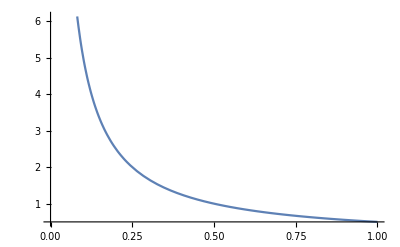

```mathematica
Plot[g[x] /(x(1-x))/. blah ,{x,0,1}]
```

```mathematica
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}]
```

{5.75584}

```mathematica
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}]
```

{{0.0868252}}

```mathematica
Print[expectation]
```

{{0.0868252}}

```mathematica
expectation  = expectation[[1]][[1]]
```

0.0868252

```mathematica
expectation = mult * expectation
```

0.0434126

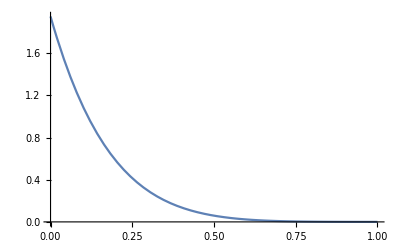

```mathematica
Plot[neutral/. {x->expectation, t->time}, {y,0,1}]
```

```mathematica
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}]
```

0.307607

```mathematica
pNeutFix = 1- neutAUC
```

0.692393

```mathematica
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}]
```

-1.95008 Max[0,0.0434126-Ψ]+5.46116 Max[0,0.0434126-Ψ]^2-8.85185 Max[0,0.0434126-Ψ]^3+9.09239 Max[0,0.0434126-Ψ]^4-6.00824 Max[0,0.0434126-Ψ]^5+2.36175 Max[0,0.0434126-Ψ]^6-0.320942 Max[0,0.0434126-Ψ]^7-0.173864 Max[0,0.0434126-Ψ]^8+0.0986925 Max[0,0.0434126-Ψ]^9-0.0166305 Max[0,0.0434126-Ψ]^10+1.95008 Min[1,0.0434126+Ψ]-5.46116 Min[1,0.0434126+Ψ]^2+8.85185 Min[1,0.0434126+Ψ]^3-9.09239 Min[1,0.0434126+Ψ]^4+6.00824 Min[1,0.0434126+Ψ]^5-2.36175 Min[1,0.0434126+Ψ]^6+0.320942 Min[1,0.0434126+Ψ]^7+0.173864 Min[1,0.0434126+Ψ]^8-0.0986925 Min[1,0.0434126+Ψ]^9+0.0166305 Min[1,0.0434126+Ψ]^10

```mathematica
thresh = Solve[tmp == (sigCutoff - pNeutFix) && 0<Ψ<1, {Ψ}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.4012}}

```mathematica
Print[thresh]
```

{{Ψ→0.4012}}

```mathematica
If[Length[thresh] != 1,Throw[{α, VG, thresh}]]
```

```mathematica
Ψ = Ψ /. thresh
```

{0.4012}

```mathematica
Print[Ψ]
```

{0.4012}

```mathematica
Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->expectation,t ->time, Ne->selectedNe Λ -> jumpSize, W->fitVar,VG->genVar},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

$Aborted

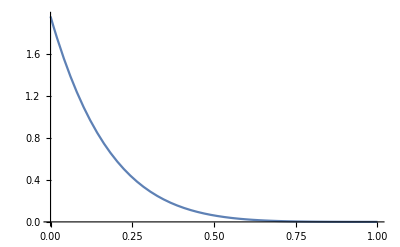

```mathematica
Plot[Evaluate[SimplifiedHayward[3]/. {x->expectation,t ->time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar}],{y,0,1}]
```

```mathematica
FindMinimum[Evaluate[SimplifiedHayward[3]/.{x->expectation,t -> 0.25, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar}],{y,0,1}]
```

{2.31126×10^-6,{y→0.9612}}

```mathematica
totalP = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{y, 0,1}]
```

0.311426

```mathematica
Pdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{y, Min[expectation+Ψ,1],1}]
```

0.0104107

```mathematica
Pnotdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

```mathematica
Clear[out];
out = {{"alpha","VG","expectation","thresh","totalP","Pdetected","Pnotdetected
"}};
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
time = 0.25;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
```

```mathematica
out
```

{{alpha,VG,expectation,thresh,totalP,Pdetected,Pnotdetected
}}

```mathematica
Do[Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected];
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe},
g,{x,0,1},MaxStepSize->.000025];
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}];
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}];
Print[expectation];
expectation  = expectation[[1]][[1]];
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}];
thresh = Solve[tmp == (sigCutoff - pNeutFix) && 0<Ψ<1, {Ψ}, Reals];
Print[thresh];
If[Length[thresh] != 1,Throw[{α, VG, thresh}]];
Ψ = Ψ /. thresh;
Print[Ψ];
totalP = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}];
Pdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Min[expectation+Ψ,1],1}];
Pnotdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}];
AppendTo[out,{α,VG,expectation,Ψ[[1]],totalP,Pdetected,Pnotdetected}],
{α, {0.00025, 0.0005, 0.00075,0.001,0.002,0.005}},
{VG, {.101, .0101, .00101}}
]
```

{{0.0868252}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.472651}}

{0.472651}

{{0.0868252}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.472651}}

{0.472651}

{{0.0868252}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
out
```

{{alpha,VG,expectation,thresh,totalP,Pdetected,Pnotdetected
},{0.00025,0.101,0.0868252,0.472651,0.526846,0.0100437,0.516802},{0.00025,0.0101,0.0868252,0.472651,0.531245,0.0104841,0.520761},{0.00025,0.00101,0.0868252,0.472651,0.53552,0.0112951,0.524225},{0.0005,0.101,0.0867269,0.472537,0.527222,0.0100875,0.517135},{0.0005,0.0101,0.0867269,0.472537,0.536023,0.0109891,0.525034},{0.0005,0.00101,0.0867269,0.472537,0.544544,0.0127323,0.531811},{0.00075,0.101,0.0865633,0.472346,0.527322,0.0101315,0.517191},{0.00075,0.0101,0.0865633,0.472346,0.540522,0.0115153,0.529007},{0.00075,0.00101,0.0865633,0.472346,0.553255,0.014323,0.538932},{0.001,0.101,0.0863348,0.472079,0.527146,0.0101756,0.516971},{0.001,0.0101,0.0863348,0.472079,0.544738,0.0120627,0.532676},{0.001,0.00101,0.0863348,0.472079,0.561644,0.0160787,0.545565},{0.002,0.101,0.0847821,0.470244,0.523666,0.0103516,0.513315},{0.002,0.0101,0.0847821,0.470244,0.558678,0.0144629,0.544215},{0.002,0.00101,0.0847821,0.470244,0.591853,0.0249896,0.566864},{0.005,0.101,0.0746142,0.457218,0.486859,0.0108527,0.476006},{0.005,0.0101,0.0746142,0.457218,0.570352,0.0234055,0.546947},{0.005,0.00101,0.0746142,0.457218,0.648419,0.0754103,0.573009}}

```mathematica
Export["alpha_VG.csv",out,"csv"];
```

```mathematica
Clear[out]
```

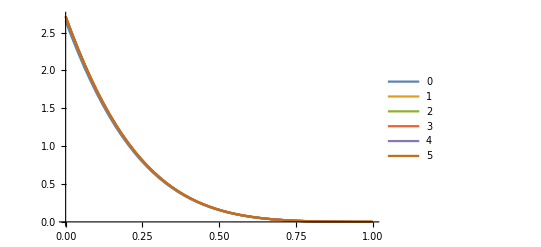

```mathematica
Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

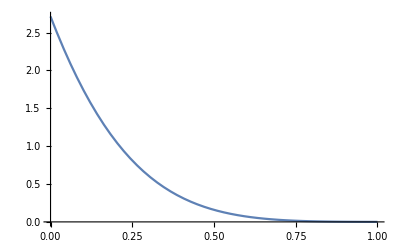

```mathematica
Plot[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y,0,1}]
```

```mathematica
totalP = Integrate[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y, 0.00001,.9999}]
```

6.87861×10^159

```mathematica
Pdetected = Integrate[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y, Min[expectation+Ψ,1],1}]
```

-1.37572×10^160

```mathematica
Pnotdetected = Integrate[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

6.87861×10^159

```mathematica
totalP = NIntegrate[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y, 0,1}]
```

0.526846

```mathematica
Pdetected = NIntegrate[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y, Min[expectation+Ψ,1],1}]
```

0.0100437

```mathematica
Pnotdetected = NIntegrate[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

0.516802

```mathematica
{α, {0.00025, 0.0005, 0.00075,0.001,0.002,0.005}},
{VG, {.101, .0101, .00101}
```

```mathematica
Clear[SourceNe]
```

```mathematica
Clear[blah];
Clear[Ne];
blah=NDSolve[{0 == ( SourceNe α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{α->.005,Λ->1,W->1, θ ->.5, SourceNe -> 20000},
g,{x,0,1},MaxStepSize->.000025];
```

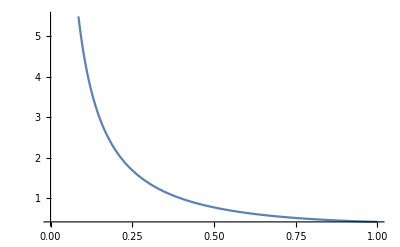

```mathematica
Plot[g[x] /(x(1-x))/. blah ,{x,0,1}]
```

```mathematica
20000*0.005^2
```

0.5

```mathematica
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}]
```

{5.52598}

```mathematica
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}]
```

{{0.0746142}}

```mathematica
expectation  = expectation[[1]][[1]]
```

0.0408214

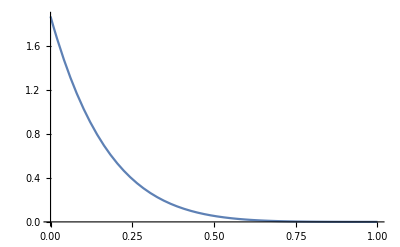

```mathematica
Plot[neutral/. {x->expectation, t->.25}, {y,0,1}]
```

```mathematica
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->.25}], {y,0,1}]
```

0.292025

```mathematica
pNeutFix = 1- neutAUC
```

0.707975

```mathematica
.99 - pNeutFix
```

0.282025

```mathematica
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->.25}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}];
```

```mathematica
thresh = Solve[tmp == (0.99 - pNeutFix) && 0<Ψ<1, {Ψ}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
thresh = {{Ψ->0.394830239061778},{Ψ->0.3}}
```

{{Ψ→0.39483},{Ψ→0.3}}

```mathematica
Length[thresh]
```

2

```mathematica
If[Length[thresh] != 1,Throw[{α, VG, thresh}]]
```

Throw::nocatch: Uncaught Throw[{α,VG,{{Ψ→0.39483},{Ψ→0.3}}}] returned to top level.

Hold[Throw[{α,VG,{{Ψ→0.39483},{Ψ→0.3}}}]]

```mathematica
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->.25}],{y, 0, expectation+Ψ}];
```

```mathematica
thresh = Solve[tmp == (0.99 - pNeutFix) && 0<Ψ<1, {Ψ}, Reals]
```

{{Ψ→0.39483}}

```mathematica
Ψ = Ψ /. thresh
```

{0.39483,0.3}

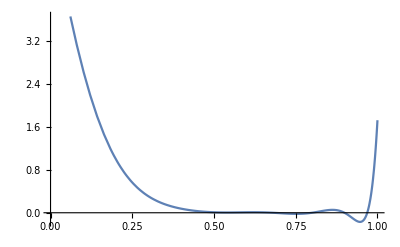

```mathematica
Plot[SimplifiedHayward[3]/.{x->expectation,t -> 0.1, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{y,0,1}]
```

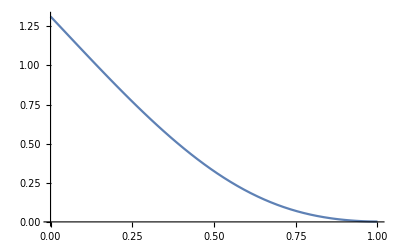

```mathematica
Plot[SimplifiedHayward[3]/.{x->expectation,t -> 0.25, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{y,0,1}]
```

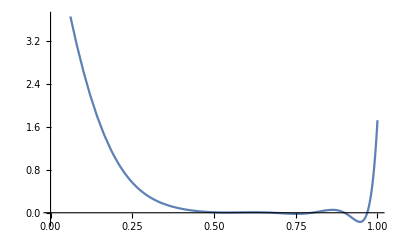

```mathematica
Plot[Evaluate[SimplifiedHayward[5]/.{x->expectation,t -> 0.1, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111}],{y,0,1}]
```

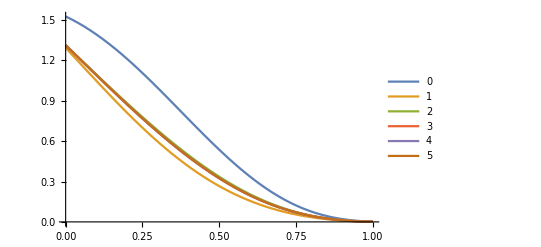

```mathematica
Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->expectation,t -> 0.25, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

```mathematica
totalP = Integrate[SimplifiedHayward[3]/.{x->expectation,t -> 0.25, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{y, 0,1}]
```

0.443845

```mathematica
Pdetected = Integrate[SimplifiedHayward[3]/.{x->expectation,t -> 0.25, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{y, Min[expectation+Ψ,1],1}]
```

0.0749551

```mathematica
(*Pdetected = Integrate[SimplifiedHayward[3]/.{x->expectation,t -> 0.25, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{y, Min[expectation+Ψ,1],0.6}]*)
```

0.0497662

```mathematica
Pnotdetected = Integrate[SimplifiedHayward[3]/.{x->expectation,t -> 0.25, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

0.36889

```mathematica
Pdetected + Pnotdetected
```

0.443845

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
time = 0.25;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
VG =.00101;
```

```mathematica
Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected]
```

```mathematica
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe,α->0.01},
g,{x,0,1},MaxStepSize->.000025]
```

{{g→InterpolatingFunction[{{0., 1.}}, <>]}}

```mathematica
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}]
```

{5.01704}

```mathematica
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}]
```

{{0.0471997}}

```mathematica
expectation  = expectation[[1]][[1]]
```

0.0471997

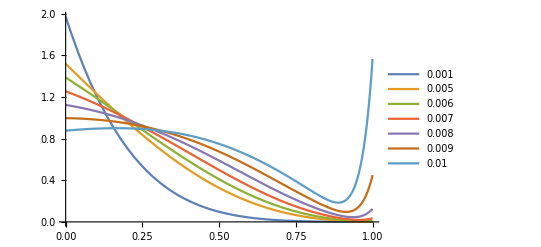

```mathematica
Plot[Evaluate[Table[SimplifiedHayward[5]/. {x->expectation,t ->time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{α, {0.001,0.005,0.006,0.007,0.008,0.0090,.01}}]],{y,0,1},PlotLegends->{ 0.001,0.005,0.006,0.007,0.008,0.0090,.01}]
```

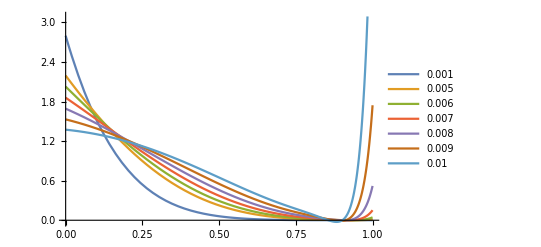

```mathematica
Plot[Evaluate[Table[SimplifiedHayward[5]/. {x->expectation,t ->0.2, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{α, {0.001,0.005,0.006,0.007,0.008,0.0090,.01}}]],{y,0,1},PlotLegends->{ 0.001,0.005,0.006,0.007,0.008,0.0090,.01}]
```

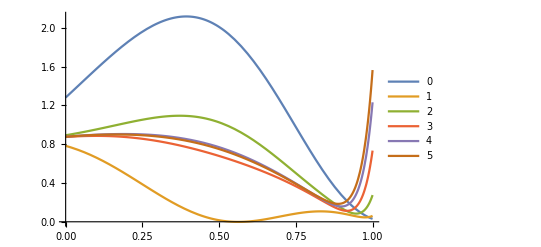

```mathematica
Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->expectation,t ->time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,α->.01},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
time = 0.25;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.005;
VG =.00101;
```

```mathematica
Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected]
```

```mathematica
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe},
g,{x,0,1},MaxStepSize->.000025]
```

{{g→InterpolatingFunction[{{0., 1.}}, <>]}}

```mathematica
Plot[g[x] /(x(1-x))/. blah ,{x,0,1}]
```

-Graphics-

```mathematica
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}]
```

{5.52598}

```mathematica
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}]
```

{{0.0746142}}

```mathematica
Print[expectation]
```

{{0.0746142}}

```mathematica
expectation  = expectation[[1]][[1]]
```

0.0746142

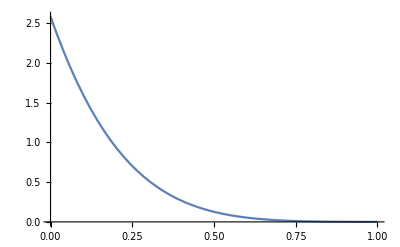

```mathematica
Plot[neutral/. {x->expectation, t->time}, {y,0,1}]
```

```mathematica
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}]
```

0.472093

```mathematica
pNeutFix = 1- neutAUC
```

0.527907

```mathematica
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}]
```

-2.58332 Max[0,0.0746142-Ψ]+5.89325 Max[0,0.0746142-Ψ]^2-6.90498 Max[0,0.0746142-Ψ]^3+3.53509 Max[0,0.0746142-Ψ]^4+1.20012 Max[0,0.0746142-Ψ]^5-3.3106 Max[0,0.0746142-Ψ]^6+2.56949 Max[0,0.0746142-Ψ]^7-1.12125 Max[0,0.0746142-Ψ]^8+0.283183 Max[0,0.0746142-Ψ]^9-0.033072 Max[0,0.0746142-Ψ]^10+2.58332 Min[1,0.0746142+Ψ]-5.89325 Min[1,0.0746142+Ψ]^2+6.90498 Min[1,0.0746142+Ψ]^3-3.53509 Min[1,0.0746142+Ψ]^4-1.20012 Min[1,0.0746142+Ψ]^5+3.3106 Min[1,0.0746142+Ψ]^6-2.56949 Min[1,0.0746142+Ψ]^7+1.12125 Min[1,0.0746142+Ψ]^8-0.283183 Min[1,0.0746142+Ψ]^9+0.033072 Min[1,0.0746142+Ψ]^10

```mathematica
thresh = Solve[tmp == (sigCutoff - pNeutFix) && 0<Ψ<1, {Ψ}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.457218}}

```mathematica
Print[thresh]
```

{{Ψ→0.457218}}

```mathematica
If[Length[thresh] != 1,Throw[{α, VG, thresh}]]
```

```mathematica
Ψ = Ψ /. thresh
```

{0.457218}

```mathematica
Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, 0,expectation,expectation+Ψ}] + pNeutFix
```

{0.99}

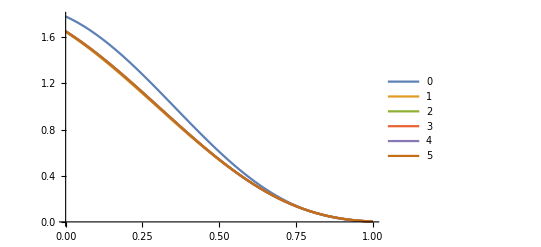

```mathematica
Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->expectation,t ->time, Ne->selectedNe,α->0.005, Λ -> jumpSize, W->fitVar},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

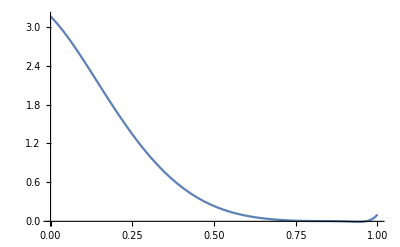

```mathematica
Plot[Evaluate[SimplifiedHayward[5]/.{x->expectation,t -> 0.15, Ne->selectedNe, Λ -> jumpSize, W->fitVar}],{y,0,1}]
```

```mathematica
FindMinimum[Evaluate[SimplifiedHayward[5]/.{x->expectation,t -> 0.15, Ne->selectedNe, Λ -> jumpSize, W->fitVar}],{y,0,1}]
```

{-0.00853182,{y→0.940591}}

```mathematica
totalP = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}]
```

0.648419

```mathematica
expectation + Ψ
```

{0.531832}

```mathematica
Pdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Min[expectation+Ψ,1],1}]
```

0.0754103

```mathematica
Pnotdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

0.573009

```mathematica
totalP = Integrate[Evaluate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar}],{y, 0,1}]
Pdetected = Integrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Min[expectation+Ψ,1],1}]
Pnotdetected = Integrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

0.648419

0.0754103

0.573009